0.547827

0.427083

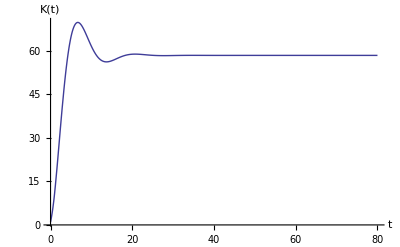

```mathematica
ClearAll;
a=0.7;
b=0.12;
τ=1;
upto=80;
A[t_]:=0;
Ca[t_]:=10;
ϵ[t_]:=0;
ArcCos[a/(a+b*τ)]
Sqrt[b *τ*(b*τ+2*a) ]
f[x_[t_]]:=x'[t]-a/τ*x[t] +(a/τ+b)*x[t-τ]-a(A[t-τ]+Ca[t-τ]+ϵ[t-τ]);
s:=NDSolve[{f[x[t]]==0,x[t/;t<0]==1},x,{t,0,upto}]
Plot[Evaluate[x[t]/.s],{t,0,upto},PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"t","K(t)"}]
```